```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation/Simulation/bin/Release"]
```

D:\work\TU\FitzHugh-Nagumo Heterogenous Networks\Simulation\Simulation\bin\Release

```mathematica
Set[#,"--"<>ToString@#]&/@{
NodeCount,
CouplingRadius,
CouplingStrength,
TimeScale,
DiffusionConstant,
DeltaTime,
WarmupTime,
MeasurementInterval,
MaximumTime,
DelayTime,
Seed,
BifurcationParameterMean,
BifurcationParameterVariance,
SpikeActivationThreshold,
SpikePeakThreshold
};
Set[#,ToString@#]&/@{
Config,
Trajectory,
InterspikeInterval
};
```

```mathematica
Read2DData[file_,type_]:=With[{n=BinaryRead[file,"Integer32"]},
Table[With[{m=BinaryRead[file,"Integer32"]},
Table[BinaryRead[file,type],{j,m}]
],{i,n}]
];
```

```mathematica
RunCommand[args__]:=RunProcess[{"Simulation.exe",args},"StandardOutput"];
GetConfig[guid_]:=Association@@(#[[1]]->ToExpression[#[[3,1]]]&/@Import["./Data/"<>guid<>"/Config.xml"][[2,3]])
GetTrajectory[guid_]:=Transpose@Read2DData["./Data/"<>guid<>"/Trajectory.bin","Real64"];
GetInterspikeInterval[guid_]:=Read2DData["./Data/"<>guid<>"/ISI.bin","Real64"];
```

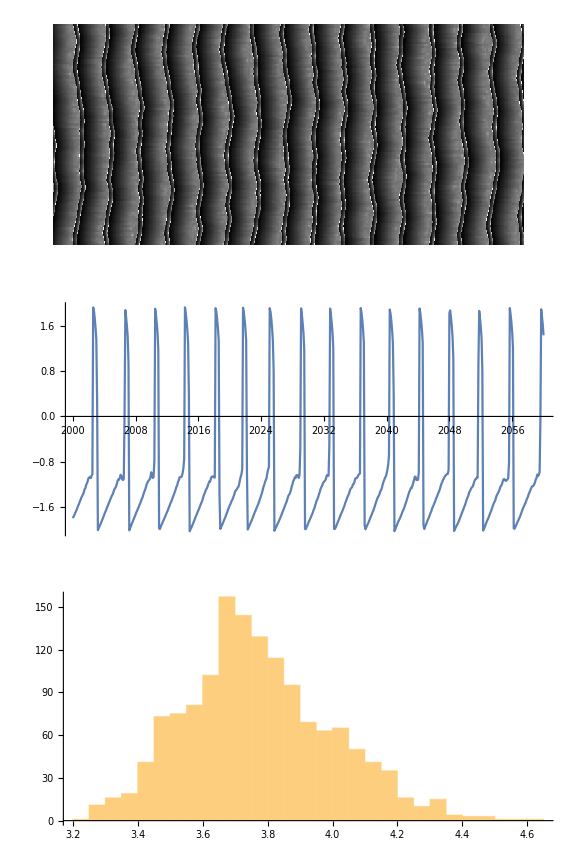

```mathematica
With[{guid=RunCommand[NodeCount,100,Config,Trajectory,InterspikeInterval]},
With[{
cfg=GetConfig@guid,
traj=GetTrajectory@guid,
isi=GetInterspikeInterval@guid},GraphicsColumn[{
ArrayPlot@traj,
ListLinePlot[traj[[1]],
PlotRange->All,
DataRange->{cfg["WarmupTime"],cfg["MaximumTime"]}
],
Histogram@Flatten@isi
},ImageSize->Large]]]
```